Following Prashant’s notes (see email May 19th 2021, “Questions about mean first passage times in your RPT papers”)

ep is E_σ and em is E_-σ, probability to escape given initial orientation σ=+1 or -1 with initial velocity v0.

```mathematica
(* Probability of exit through right boundary *)
solProb=DSolve[{v0 ep'[x]-λ ep[x]+λ em[x]==0,- v0 em'[x]-λ em[x]+λ ep[x]==0,ep[L]==1,em[0]==0},{ep[x],em[x]},x]
```

{{em[x]→(x λ)/(v0+L λ),ep[x]→(v0+x λ)/(v0+L λ)}}

```mathematica
FortranForm[ep[x]/.solProb]
```

List((v0 + x*λ)/(v0 + L*λ))

```mathematica
L0=400;
λ0=1/.27;
v00=121;
probabiliyRightPositive=Plot[ep[x]/.solProb/.λ->λ0/.L->L0/.v0->v00,{x,0,L0}];
probabiliyRightNegative=Plot[em[x]/.solProb/.λ->λ0/.L->L0/.v0->v00,{x,0,L0},PlotStyle->Red];
```

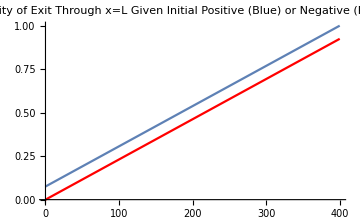
-Graphics-ProbabilityPosition

```mathematica
Labeled[Show[probabiliyRightNegative,probabiliyRightPositive,PlotRange->All,PlotLabel->"Probability of Exit Through x=L  Given Initial\nPositive (Blue) or Negative (Red) Velocity",ImageSize->Medium,LabelStyle->Directive[FontSize->15]],{"Probability","Position"},{Left,Bottom},RotateLabel->True]
```

qp is the weighted mean first passage time, i.e., S(x_0,t):=E_σ(x_0,t)T_σ(x_0,t). qm is the opposite orientation

```mathematica
solMFPT=DSolve[{v0 qp'[x]-λ qp[x]+λ qm[x]== -(v0+x λ)/(v0+L λ),
- v0 qm'[x]-λ qm[x]+λ qp[x]== -(x λ)/(v0+L λ),
qp[L]==0,qm[0]==0},{qp[x],qm[x]},x]
```

{{qm[x]→(3 L v0^2 x λ+3 L^2 v0 x λ^2-v0 x^3 λ^2+L^3 x λ^3-L x^3 λ^3)/(3 v0^2 (v0+L λ)^2),qp[x]→(3 L v0^3-3 v0^3 x+3 L^2 v0^2 λ-3 v0^2 x^2 λ+L^3 v0 λ^2+3 L^2 v0 x λ^2-3 L v0 x^2 λ^2-v0 x^3 λ^2+L^3 x λ^3-L x^3 λ^3)/(3 v0^2 (v0+L λ)^2)}}

```mathematica
TeXForm[FullSimplify[qp[x]/.solMFPT]]
```

\left\{\frac{(L-x) \left(\lambda ^2 \text{v0} \left(L^2+4 L x+x^2\right)+3 \lambda  \text{v0}^2 (L+x)+\lambda ^3 L x (L+x)+3 \text{v0}^3\right)}{3 \text{v0}^2 (\lambda 
   L+\text{v0})^2}\right\}

```mathematica
TeXForm[FullSimplify[qm[x]/.solMFPT]]
```

\left\{\frac{\lambda  x \left(\lambda  \text{v0} \left(3 L^2-x^2\right)+3 L \text{v0}^2+\lambda ^2 L (L-x) (L+x)\right)}{3 \text{v0}^2 (\lambda  L+\text{v0})^2}\right\}

Once we have qp and qm, divide each by corresponding ep and em, respectively.

```mathematica
meanTimeRightPos=Plot[qp[x]/((v0+x λ)/(v0+L λ))/.solMFPT/.λ->λ0/.L->L0/.v0->v00,{x,0,L0}];
meanTimeRightNeg=Plot[qm[x]/((x λ)/(v0+L λ))/.solMFPT/.λ->λ0/.L->L0/.v0->v00,{x,0,L0},PlotStyle->Red];
```

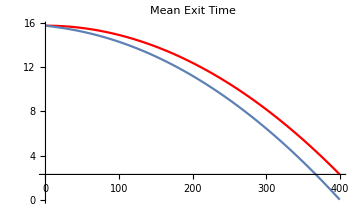
-Graphics-TimePosition

```mathematica
Labeled[Show[meanTimeRightNeg,meanTimeRightPos,PlotRange->All,PlotLabel->"Mean Exit Time",ImageSize->Medium,LabelStyle->Directive[FontSize->15]],{"Time","Position"},{Left,Bottom},RotateLabel->True]
```

Equations in full

```mathematica
(* time to escape right given initial positive velocity. *)
TeXForm[FullSimplify[qp[x]/((v0+x λ)/(v0+L λ))/.solMFPT]]
```

\left\{\frac{1}{3} \left(\frac{\lambda  (L-x) (L+x)}{\text{v0}^2}+\frac{L}{\lambda  L+\text{v0}}+\frac{2 (L-x)}{\text{v0}}-\frac{x}{\text{v0}+\lambda  x}\right)\right\}

```mathematica
(* Time to escape right given initial negative velocity *)
TeXForm[FullSimplify[qm[x]/((x λ)/(v0+L λ))/.solMFPT]]
```

\left\{\frac{1}{3} \left(\frac{\lambda  (L-x) (L+x)}{\text{v0}^2}+\frac{L}{\lambda  L+\text{v0}}+\frac{2 L}{\text{v0}}\right)\right\}

```mathematica
FortranForm[1/3 ((2 (L-x))/v0+((L-x) (L+x) λ)/v0^2+L/(v0+L λ)-x/(v0+x λ))]
```

((2*(L - x))/v0 + ((L - x)*(L + x)*λ)/v0**2 + L/(v0 + L*λ) - x/(v0 + x*λ))/3.

## MFPT starting at origin and different domain lengths

```mathematica
e0p=Limit[ep[x]/.solProb,x->0][[1]]
```

v0/(v0+L λ)

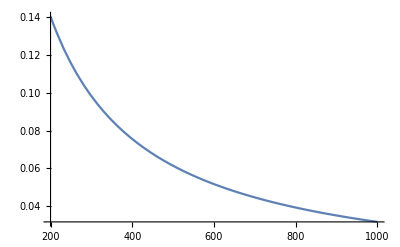

```mathematica
Plot[e0p/.λ->λ0/.v0->v00,{L,200,1000}]
```

```mathematica
mfpt0p=Limit[qp[x]/((v0+x λ)/(v0+L λ))/.solMFPT,x->0][[1]]
mfpt0m=Limit[qm[x]/((x λ)/(v0+L λ))/.solMFPT,x->0][[1]]
```

(3 L v0^3+3 L^2 v0^2 λ+L^3 v0 λ^2)/(3 v0^3 (v0+L λ))

(3 L v0^2 λ+3 L^2 v0 λ^2+L^3 λ^3)/(3 v0^3 λ+3 L v0^2 λ^2)

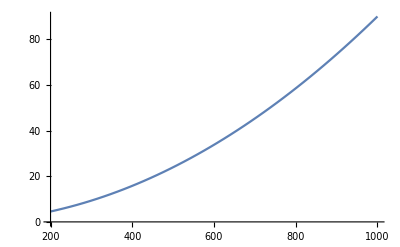

```mathematica
Plot[mfpt0p/.λ->λ0/.v0->v00,{L,200,1000}]
```

```mathematica
FortranForm[mfpt0p]
```

(3*L*v0**3 + 3*L**2*v0**2*λ + L**3*v0*λ**2)/(3.*v0**3*(v0 + L*λ))

```mathematica
FortranForm[qp[x]/.solMFPT]
```

List((3*L*v0**3 - 3*v0**3*x + 3*L**2*v0**2*λ - 3*v0**2*x**2*λ + L**3*v0*λ**2 + 3*L**2*v0*x*λ**2 - 3*L*v0*x**2*λ**2 - v0*x**3*λ**2 + L**3*x*λ**3 - L*x**3*λ**3)/
     -   (3.*v0**2*(v0 + L*λ)**2))